### x_C-x_D dynamics

```mathematica
yYn[c1_,c2_,X0_,Y0_,e_]:=Module[
{x,y,γ,δ,CC,β,α,κ,nn,sol,xT,yT},
Clear[sol,x,y,t];
γ=1.0;
δ=0.1;
CC=1000.;
β=5.0;
α=2.0;
κ=0.5;
nn[Y_,λ_,ν_]:=If[e==False,λ+ν Y/CC,Exp[λ+ν Y/CC]];
sol[ν_,λ_]:=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(nn[x[t]+y[t],λ,ν]-1))/nn[x[t]+y[t],λ,ν]-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(nn[x[t]+y[t],λ,ν]-1))/nn[x[t]+y[t],λ,ν]-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==X0,y[0]==Y0
},{x,y},{t,100000}];


xT=x[100000]/.sol[c1,c2]⟦1⟧;
yT=y[100000]/.sol[c1,c2]⟦1⟧;

{Round[xT/(xT+yT),1/CC],xT+yT,nn[xT+yT,c1,c2]}

]

t0={#,yYn[0,#,100,100,True]}&/@Range[0,Log[40],0.01];
```

```mathematica
t1={#,yYn[0.5,#,100,100,True]}&/@Range[0,Log[40],0.01];
```

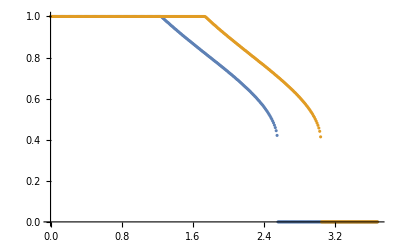

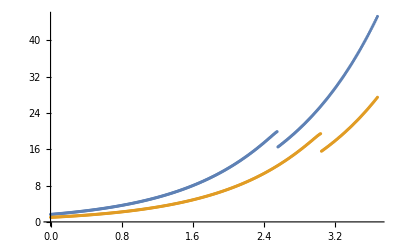

```mathematica
ListPlot[
{
{t1⟦#,1⟧,t1⟦#,2,1⟧}&/@Range[1,t1//Length,1],
{t0⟦#,1⟧,t0⟦#,2,1⟧}&/@Range[1,t0//Length,1]
}
]
ListPlot[
{
{t1⟦#,1⟧,t1⟦#,2,3⟧}&/@Range[1,t1//Length,1],
{t0⟦#,1⟧,t0⟦#,2,3⟧}&/@Range[1,t0//Length,1]
}
]
```

### x_C-x_D-n dynamics

#### time series

```mathematica
yYn[X0_,Y0_,N0_,ν_,λ_,T_]:=Module[
{x,y,n,γ,δ,CC,β,α,κ,nn,sol,xT,yT,t},
Clear[sol,x,y,n,t];
γ=1.0;
δ=0.9;
CC=1000.;
β=5.0;
α=2.0;
κ=0.5;
sol=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n[t]-1))/n[t]-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n[t]-1))/n[t]-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
,
n'[t]==ν n[t](1-λ n[t]/(x[t]+y[t]))
, x[0]==X0,y[0]==Y0,n[0]==N0
},{x,y,n},{t,T*1.05}];

Flatten[{#,{x[#]/CC,y[#]/CC,n[#]/CC}/.sol},1]&/@Range[0,T,0.01]
]
TIME=200;
t0=yYn[100,1,10,0,1,TIME];

t1=yYn[100,10 ,100,0,10,TIME];

t2=yYn[100,10,100,1.,10,TIME];
```

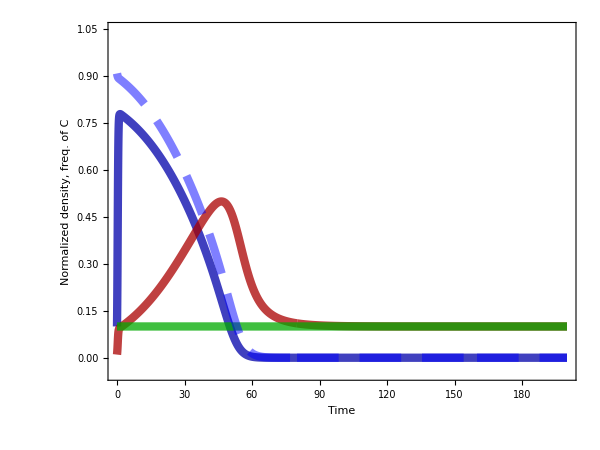

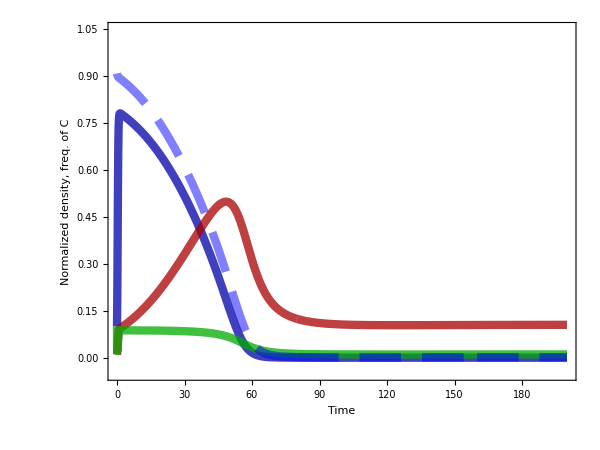

```mathematica
lp[t0_]:=ListPlot[
{
{t0⟦#,1⟧,t0⟦#,2,1⟧}&/@Range[1,t0//Length,1],
{t0⟦#,1⟧,t0⟦#,2,2⟧}&/@Range[1,t0//Length,1],
{t0⟦#,1⟧,t0⟦#,2,3⟧}&/@Range[1,t0//Length,1],
{t0⟦#,1⟧,t0⟦#,2,1⟧/(t0⟦#,2,1⟧+t0⟦#,2,2⟧)}&/@Range[1,t0//Length,1]
}
,PlotStyle->{
{Thickness[0.01],Opacity[0.75,Darker[Blue]]},
{Thickness[0.01],Opacity[0.75,Darker[Red]]},
{Thickness[0.01],Opacity[0.75,Darker[Green]]},
{Thickness[0.01],Dashing[{0.05,0.025}],Opacity[0.5,Blue]}
}
,Joined->True
,PlotRange->{All,{-0.05,1.05}}
,Frame->True
,ImageSize->600
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Time","Normalized density, freq. of C"}
]


Show[lp[t1]]
Show[lp[t2]]
```

```mathematica
t3=yYn[100,10,800,1.,40.,TIME];
Last[t3]⟦2,3⟧1000.
Show[lp[t3]]
```

22.5

-Graphics-

#### Endpoints

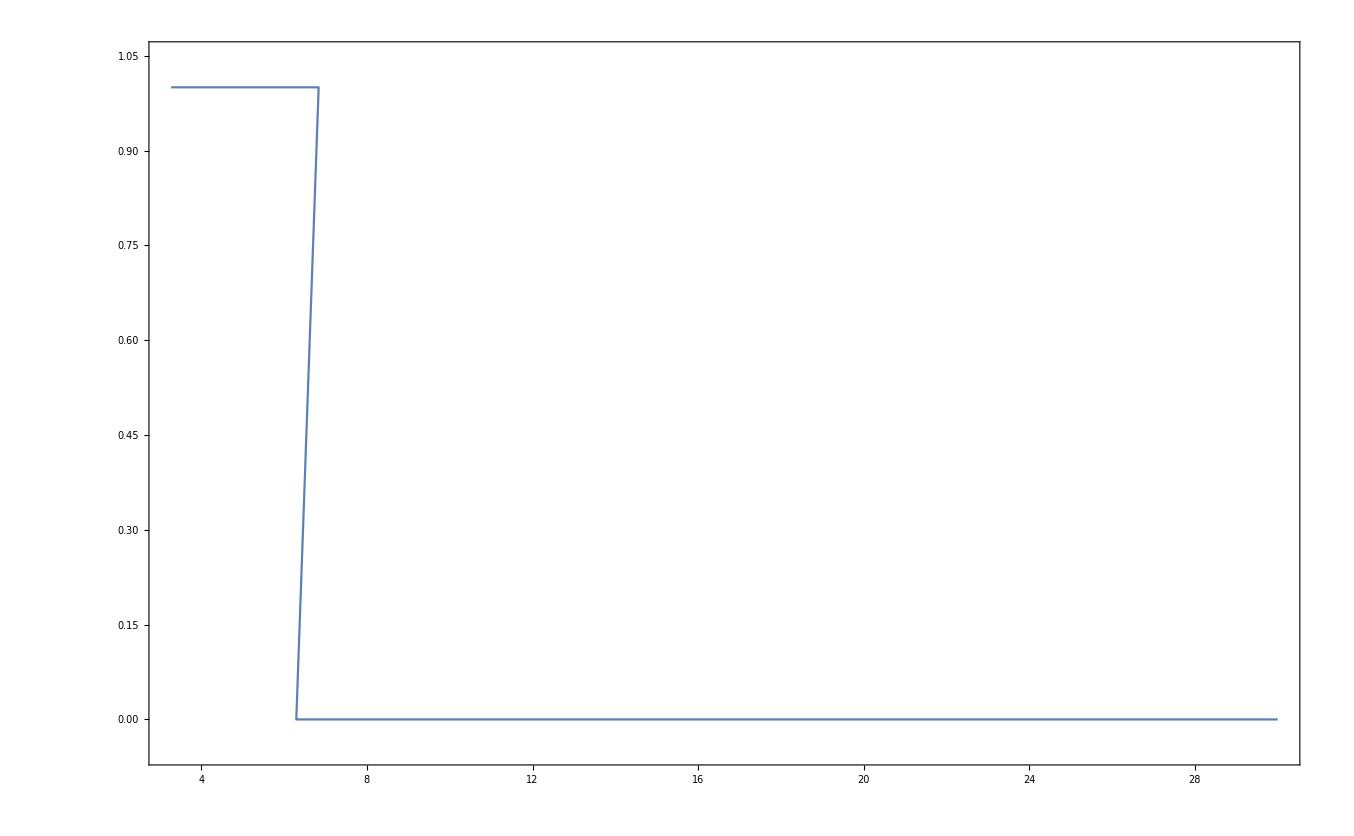

```mathematica
yYnFinal[X0_,Y0_,N0_,ν_,λ_,T_]:=Module[
{x,y,n,γ,δ,CC,β,α,κ,nn,sol,xT,yT,t},
Clear[sol,x,y,n,t];
γ=1.0;
δ=0.1;
CC=1000.;
β=2.0;
α=3.0;
κ=0.5;
sol=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n[t]-1))/n[t]-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n[t]-1))/n[t]-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
,
n'[t]==ν n[t](1-λ n[t]/(x[t]+y[t]))
, x[0]==X0,y[0]==Y0,n[0]==N0
},{x,y,n},{t,T*1.05}];

Flatten[{n[T]/.sol,Round[x[T]/(x[T]+y[T])/.sol,1/CC]},1]
]

list=yYnFinal[1,100,15,10,#,15500.]&/@Range[30,300,0.5];

ListPlot[
list
,Frame->True
,PlotRange->{All,{-0.05,1.05}},Joined->True
]
```

### n_C and n_D

#### Dynamics

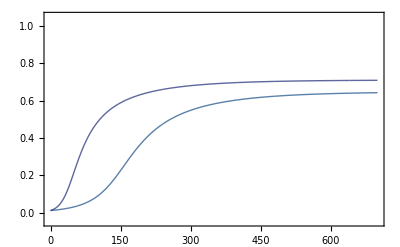

```mathematica
nCnDinvasion[X0_,nC_,nD_,T_]:=Module[
{x,y,n,γ,δ,CC,β,α,κ,nn,sol,xT,yT,t},
Clear[sol,x,y,n,t];
γ=1.0;
δ=0.1;
CC=1000.;
β=5.0;
α=2.0;
κ=0.5;
sol=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(nC-1))/nC-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(nD-1))/nD-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==X0,y[0]==CC(1-δ/γ)
},{x,y},{t,T*1.05}];

Flatten[{#,{x[#]/CC,x[#]/(x[#]+y[#]),y[#]/CC}/.sol},1]&/@Range[0,T,0.01]
]
lp[nC_,nD_]:=Module[{list},
list=nCnDinvasion[10,nC,nD,700];
ListPlot[
{list⟦#,1⟧,list⟦#,2,2⟧}&/@Range[1,list//Length,1]
,PlotRange->{All,{-0.05,1.05}}
,Frame->True
,Joined->True
,PlotStyle->{Thick,Opacity[0.7,ColorData["BlueGreenYellow"][(nC/nD)^1.5]]}
]
]

Show[
lp[8,25],lp[5,25]
]
```

```mathematica
list1=nCnDinvasion[10,10,30,1700];
list2=nCnDinvasion[10,5,30,1700];
ListPlot[
{
{list2⟦#,1⟧,list2⟦#,2,2⟧}&/@Range[1,list2//Length,1],{list1⟦#,1⟧,list1⟦#,2,2⟧}&/@Range[1,list1//Length,1]
}
,PlotRange->{700{-0.05,1.05},{-0.05,1.05}}
,Frame->True
,Joined->True
,PlotStyle->{{Thick,Opacity[0.7,ColorData["BlueGreenYellow"][0.6]]},{Dashed,Thick,Opacity[0.7,ColorData["BlueGreenYellow"][0.3]]}}
,ImageSize->400
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameLabel->{{"Frequency of C",None},{"Time [days]",None(*"n=8, σ=β/2"*)}}
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
,PlotLegends->{Placed[{"n_D=30, n_C=5","n_D=30, n_C=10"},{0.3,0.85}]}
]
```

-Graphics-

#### Endpoint

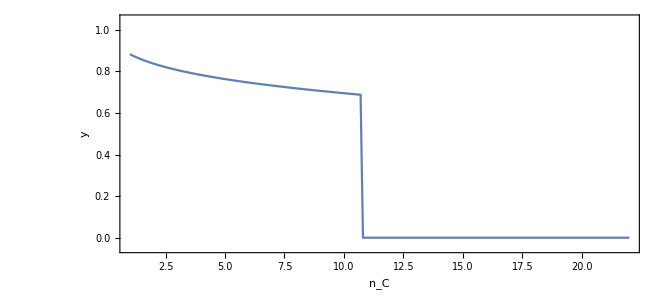

```mathematica
nCnDinvasionE[X0_,nC_,nD_,T_]:=Module[
{x,y,n,γ,δ,CC,β,α,κ,nn,sol,xT,yT,t},
Clear[sol,x,y,n,t];
γ=1.0;
δ=0.9;
CC=1000.;
β=5.0;
α=2.0;
κ=0.5;
sol=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(nC-1))/nC-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(nD-1))/nD-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==X0,y[0]==CC(1-δ/γ)-X0
},{x,y},{t,T*1.05}];

Flatten[x[T]/(x[T]+y[T])/.sol,1]⟦1⟧
]

l={#,nCnDinvasionE[1,#,15,100000]}&/@Range[1,22,0.1];

ListPlot[
l
,PlotRange->{All,{-0.05,1.05}}
,Frame->True
,Joined->True
(*,PlotStyle->{Thick,Opacity[0.7,ColorData["BlueGreenYellow"][(nC/nD)^1.5]]}*)
,ImageSize->666
,LabelStyle->{FontSize->22,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.45
,FrameLabel->{{"y",None},{"n_C",None(*"n=8, σ=β/2"*)}}
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
]
```